```mathematica
ClearAll["Global`*"]
```

```mathematica
Q1=P3 μ1+p γ1 μ2;Q2=(P2 P3 P4-(-1+p) P3 γ1 (P4+γ2)+p P2 γ1 (P4+γ3))νh;Q3=(1-p) γ1 P3+k p γ1 P2+P2 P3;
P5=dh+νh;P1=γ1+μ1+dh;P2=γ2+dh;P3=γ3+μ2+dh;P4=ρ+dh;P6=dm+νm;
```

```mathematica
(*先确定坐标位置*)
```

```mathematica
dm0=(a c dh Q3)/(P2 Q1);
dm1=(a c νh dh P4 Q3)/(νh P2 P4 Q1-dh (P1 P2 P3 P4+Q2));
dm2=(a c dh P4 Q3 νh (P2 P4 Q1 νh-dh (P1 P2 P3 P4+Q2)))/(dh^2 (P1 P2 P3 P4+Q2)^2+P2^2 P4^2 Q1^2 νh^2);
```

```mathematica
(*若dm1>0, 则dm1>dm0>dm2*)
(*若dm1<0, 则dm2<0*)
```

```mathematica
dm1-dm0;
```

```mathematica
dm0-dm2;
```

```mathematica
(*定义曲线*)
```

```mathematica
C0=(Ah dm^2 P1 P2 P3 P5 P6)/(a^2 b c dh Q3 νh νm);C1=(Ah dm P1 P2 P3 P4 P5 P6 (2 dm P2 Q1-a c dh Q3))/(a^2 b c dh Q3 (dh (P1 P2 P3 P4+Q2)+P2 P4 Q1 νh) νm);C11=(Ah dm P1 P2 P3 P4 P5 P6 ((P1 P2 P3 P4+Q2) (2 dm P2 Q1-a c dh Q3)+a c P2 P4 Q1 Q3 νh))/(a^2 b c Q3 (dh (P1 P2 P3 P4+Q2)+P2 P4 Q1 νh)^2 νm);
{a2,a1,a0}={Ah P2 P3 P4 (Ah dm^2 P1 P2 P3 P5 P6-a^2 Am b c dh Q3 νh νm),Ah dm P1 P2 P3 P4 P5 P6 (-2 dm P2 Q1+a c dh Q3)+a^2 Am b c dh Q3 (dh (P1 P2 P3 P4+Q2)+P2 P4 Q1 νh) νm,dm P1 P2 P4 P5 P6 Q1 (dm P2 Q1-a c dh Q3)};
delta=a1^2-4*a0*a2;
{b2,b1,b0}=CoefficientList[delta,Am];
Cplus=(-b1+√(b1^2-4*b0*b2))/(2 b0);
Cminus=(-b1-√(b1^2-4*b0*b2))/(2 b0);
```

```mathematica
(*设置参数*)
```

```mathematica
data={a->0.1,Ah->0.5,b->0.022,c->0.14,dh->0.000000358,k->0.5,p->0.70433,γ1->0.33,γ2->1.0035,γ3->0.0357,μ1->0.000018,μ2->0.000018,νh->0.2,νm->0.083,ρ->0.0027};
ndm0=dm0/.data
ndm1=dm1/.data
ndm2=dm2/.data
{f1,f2,f3,f4,f5}={C0,C1,C11,Cplus,Cminus}/.data;
```

0.000161374

0.000247566

0.0000938177

```mathematica
C0/.dm->ndm1/.data
```

211.434

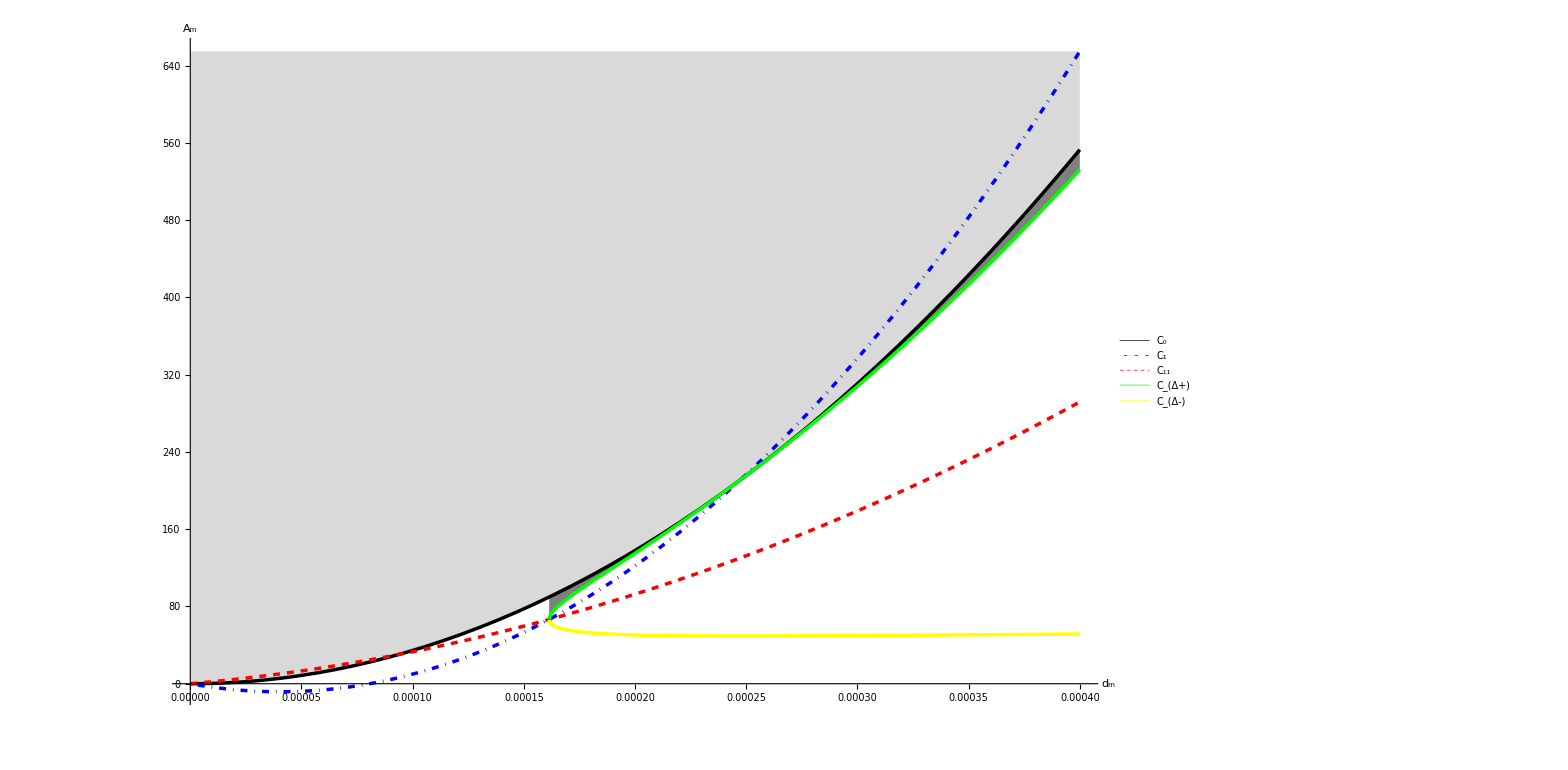

```mathematica
fig1=Plot[{f1,f2,f3,f4,f5},{dm,0,0.0004},PlotStyle->{{Black,Thickness[0.002]},{Blue,DotDashed,Thickness[0.002]},{Red,Dashed,Thickness[0.002]},{Green,Thickness[0.002]},{Yellow,Thickness[0.002]}},AxesOrigin->{0,0},AxesLabel->{"d_m","A_m"},PlotLegends->Placed[LineLegend[Automatic,{"C_0","C_1","C_11","C_(Δ+)","C_(Δ-)"},LegendLayout->{"Column",1},LabelStyle->12],{0.15,0.81}],BaseStyle->{FontFamily->"Times",FontSize->20},AxesStyle->Thickness[0.002],PlotRange->All,Filling->{{1->{{4},{None,Gray}}},{1->{Top,{LightGray}}}}]
```